Calculate density profile in an isothermal self-gravitating atmosphere.  Requires setting inner and outer boundary conditions.  NDSolve couldn’t robustly handle this.  Perhaps a shooting method would work better.

```mathematica
Exit
```

```mathematica
n = 20;
θ0 = 10^-10.;
θc = 26;
sol = NDSolve[{r^2 S''[r] + 2 r S'[r] == - θ0 Exp[S[r]] r^2,S'[1] == -θc, S[n θc] ==0},S,r,MaxSteps-> 100000,PrecisionGoal-> ∞][[1]]
θ0/θc NIntegrate[Exp[S[r]] r^2 /. sol,{r,1,θc}]
nsg = NDSolve[{r^2 S'[r] == - θc, S[n θc] ==0},S,{r,1,n θc}][[1]]
θ0/θc NIntegrate[Exp[S[r]] r^2 /. nsg,{r,1,θc}]
```

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

NDSolve::berr: There are significant errors {0.384688, -0.403104} in the boundary value residuals. Returning the best solution found.

{S→InterpolatingFunction[{{1.,520.}},<>]}

0.0413045

{S→InterpolatingFunction[{{1.,520.}},<>]}

0.0328579

```mathematica
sol = NDSolve[{r^2 S''[r] + 2 r S'[r] == - θ0 Exp[S[r]] r^2,S'[1] == -θc, S[n θc] ==0},S,r,MaxSteps-> 100000,PrecisionGoal-> ∞][[1]]
```

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

NDSolve::berr: There are significant errors {0.384688, -0.403104} in the boundary value residuals. Returning the best solution found.

{S→InterpolatingFunction[{{1.,520.}},<>]}

InterpolatingFunction::dmval: Input value {0.693261} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::unfl: Underflow occurred in computation.

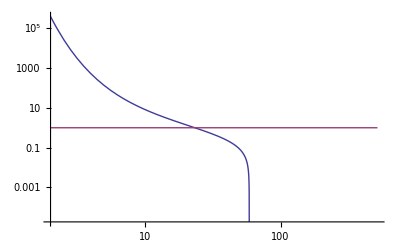

```mathematica
LogLogPlot[{Exp[S[r]]-1/. sol,1},{r,2,n θc},PlotRange->All]
```

```mathematica
?NDSolve
```

NDSolve[eqns,y,{x,x_min,x_max}] finds a numerical solution to the ordinary differential equations eqns for the function y with the independent variable x in the range x_min to x_max. 
NDSolve[eqns,y,{x,x_min,x_max},{t,t_min,t_max}] finds a numerical solution to the partial differential equations eqns. 
NDSolve[eqns,{y_1,y_2,…},{x,x_min,x_max}] finds numerical solutions for the functions y_i.

```mathematica
280/5^(1/2.)
```

125.22

```mathematica
Clear[θc]
Plot[NIntegrate[Exp[S[r]] r^2 /.  NDSolve[{r^2 S''[r] + 2 r S'[r] == θ0,S'[1] == -θc, S[n θc] ==0},S,r][[1]],{r,1,θc}],{θc,30,50}]
```

$Aborted

```mathematica
θ0
```

1/10000000000000000

```mathematica
th1 = 40.;th2 = 60;nth = 20;
θcarr = Table[th1 + (i-1)/(nth-1)(th2-th1),{i,1,nth}];
marr = Table[0,{i,1,nth}];
Do[{θc = θcarr[[i]],
sol = NDSolve[{r^2 S''[r] + 2 r S'[r] == θ0,S'[1] == -θc, S[n θc] ==0},S,r][[1]],
marr[[i]] = θ0/θc NIntegrate[Exp[S[r]] r^2 /. sol,{r,1,θc}]}
,{i,1,nth}];
```

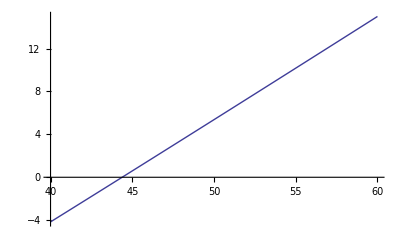

```mathematica
ListPlot[Table[{θcarr[[i]],Log[marr[[i]]]},{i,nth}],Joined->True]
```

## Adiabatic Case

```mathematica
Exit
```

```mathematica
c  = 0.1;Rc = .01;Tc =  130.;rmax = 1.6
Tsol = T /. NDSolve[{r^2 T''[r] + 2 r T'[r] == - c T[r]^(5/2)r^2,T'[Rc] == -1/Rc^2,T[Rc] == Tc},T,{r,Rc,rmax}][[1]]
```

1.6

NDSolve::mxst: Maximum number of 10000 steps reached at the point r == 1.43963.

InterpolatingFunction[{{0.01,1.43963}},<>]

```mathematica
rmax = FindRoot[Re[Tsol[r]] == 0,{r,.5}][[1,2]]
```

1.34437

```mathematica
rmax = 1.5;
Tsol[rmax]
```

0.00741408-7.88626×10^-13 ⅈ

```mathematica
Ma  = NIntegrate[c Re[Tsol[r]]^(5/2)r^2,{r,Rc,rmax}]
```

11.4827

InterpolatingFunction::dmval: Input value {-4.60507} lies outside the range of data in the interpolating function. Extrapolation will be used.

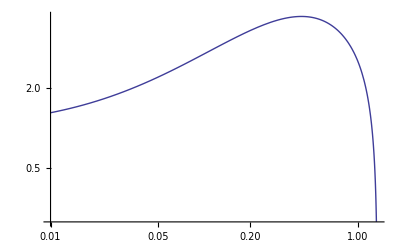

```mathematica
LogLogPlot[{Re[Tsol[r]] r},{r,.01,rmax}]
```

InterpolatingFunction::dmval: Input value {-4.60507} lies outside the range of data in the interpolating function. Extrapolation will be used.

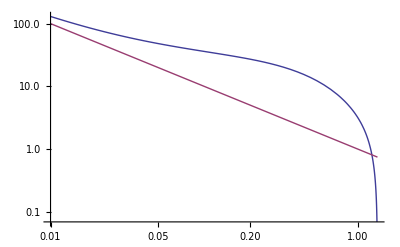

```mathematica
LogLogPlot[{Tsol[r], 1/r},{r,Rc,rmax}]
```

InterpolatingFunction::dmval: Input value {-4.60507} lies outside the range of data in the interpolating function. Extrapolation will be used.

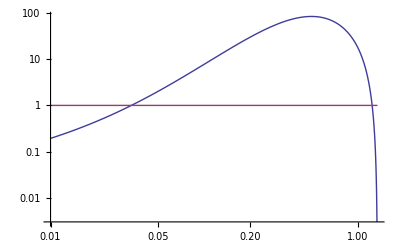

```mathematica
LogLogPlot[{Tsol[r]^2.5 r^3,1} ,{r,Rc,rmax}]
```

```mathematica
Tsol'[0.5]
```

-9.11536

```mathematica
ni = 100;
rarr = Table[Rc + (i-1)/(ni - 1)(rmax-Rc),{i,ni}];
DelAd = Table[{rarr[[i]],-Tsol'[rarr[[i]]]rarr[[i]]^2/(1+Mar[rarr[[i]]])},{i,ni}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in rr near {rr} = {0.85955189688607429483735433706215189886279404163360595703125}. NIntegrate obtained 0.0714725  - 1.2447×10^-6\ ⅈ
 and 7.29127×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in rr near {rr} = {0.86152777119628960213193469286352410563267767429351806640625}. NIntegrate obtained 0.0714725  + 1.34443×10^-6\ ⅈ
 and 0.0000103962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in rr near {rr} = {0.8678295183896437003934209997169091366231441497802734375}. NIntegrate obtained 0.0714725  + 8.52577×10^-6\ ⅈ
 and 5.76079×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

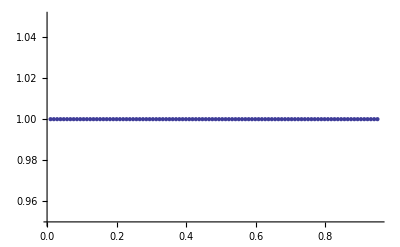

```mathematica
ListPlot[Re[DelAd],PlotRange->{0.95,1.05}]
```

```mathematica
Mar[0.1]
```

Integrate::ilim: Invalid integration variable or limit(s) in 0.1.

0.1 ∫(2.48773+0. ⅈ)ⅆ0.1

```mathematica
Clear[Mar]
```

```mathematica
Mar[r_] := Re[NIntegrate[c Tsol[rr]^(5/2)rr^2,{rr,Rc,r}]]
```

```mathematica
Mar[.5]
```

0.070958

```mathematica
Tint[r_] = Integrate[Tsol[r],r]
```

InterpolatingFunction[{{0.01,0.971908}},<>][r]

```mathematica
Tint[.5]
```

3.37132+0. ⅈ

```mathematica
Tsol
```

InterpolatingFunction[{{0.01,0.971908}},<>]

```mathematica
Mar[r_] = Integrate[c Tsol[r]^(5/2)r^2,r]
Ma  = NIntegrate[c Re[Tsol[r]]^(5/2)r^2,{r,Rc,rmax}]
```

0.1 ∫r^2 (InterpolatingFunction[{{0.01,3.7}},<>][r])^(5/2)ⅆr

6.97186+0.00223777 ⅈ

```mathematica
Mar[x]
```

0.1 ∫x^2 (InterpolatingFunction[{{0.01,0.971908}},<>][x])^(5/2)ⅆx

```mathematica
Integrate[Tsol[r],r]
```

InterpolatingFunction[{{0.01,0.971908}},<>][r]

```mathematica
NIntegrate[T[r]^2.5 r^3 /. sol,{r,Rc,.5}]
```

32.1143+0. ⅈ

```mathematica
DSolve[{2 r T'[r]+r^2 T''[r]==-c T[r]^(5/2)r^2},T,r]
```